# MuRF Envelope Curve

This notebook demonstrates creates a MuRF envelope curve.
Copyright © Terje B. 2011

```mathematica
MurfEnvelope[pmaxelements_Integer, ppotpos_] :=
Module[{},
refvoltage=5;
maxpotpos=10;
convpotpos=ppotpos;
If [ppotpos>5, convpotpos=10-ppotpos];
If [ppotpos<5,
(
risepercent=50-(((5-convpotpos)*50)/(maxpotpos/2));
fallpercent=50-(((5-convpotpos)*34)/(maxpotpos/2));
risepercent=50-(((50-(ppotpos*10))^2)/50);
fallpercent=50-(((50-(ppotpos*10))^2)/75);
),
(
risepercent=50-(((5-convpotpos)*34)/(maxpotpos/2));
fallpercent=50-(((5-convpotpos)*50)/(maxpotpos/2));
risepercent=50-(((50-(ppotpos*10))^2)/75);
fallpercent=50-(((50-(ppotpos*10))^2)/50);
)
];

maxelements=pmaxelements;
maxelementsrise=Round[(maxelements*risepercent)/100];
maxelementsfall=Round[(maxelements*fallpercent)/100];

If [maxelementsrise<1, maxelementsrise=1];
If [maxelementsfall<1, maxelementsfall=1];

If [maxelementsrise+maxelementsfall>maxelements,
maxelementsfall=maxelementsfall-1];

riseinterval=refvoltage/maxelementsrise;
fallinterval=refvoltage/maxelementsfall;
curvedata=ConstantArray[0, maxelements+1];
change=0;
counter=0;
curvedata[[1]]=0;

If [ppotpos>5,
(
startpos=maxelements-(maxelementsrise+maxelementsfall);
If [startpos<1,startpos=2]
),
startpos=2
];

For [counter=startpos,counter < (startpos+maxelementsrise), counter++,
change=change+riseinterval;
If [change>refvoltage, change=refvoltage];
curvedata[[counter]]=change;
];

tempcounter=counter;

For[counter=tempcounter, counter < (maxelementsfall+tempcounter-1), counter++,
change=change-fallinterval;
If [change>0, curvedata[[counter]]=change, curvedata[[counter]]=0
];
];
curvedata
]
```

Test the module:

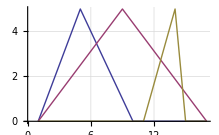

{0.,0.625,1.25,1.875,2.5,3.125,3.75,4.375,5.,4.375,3.75,3.125,2.5,1.875,1.25,0.625,0.}

```mathematica
curveData1 = MurfEnvelope[16, 1.55];
curveData2 = MurfEnvelope[16, 5];
curveData3 = MurfEnvelope[16, 10];

ListLinePlot[{curveData1, curveData2, curveData3},  PlotRange->Automatic,
GridLines->Automatic, GridLinesStyle->LightGray]
N[curveData2]
```

Animate and control the MurfEnvelope module with the MANIPULATE command:

```mathematica
Manipulate[
curveDataDisplay = MurfEnvelope[maxElements, envelopePos];

ListLinePlot[curveDataDisplay,  PlotStyle->Blue, GridLines->Automatic, GridLinesStyle->LightGray, PlotRange->{{0, maxElements + 1}, {0, 5}}, Filling->Axis, PlotMarkers->Automatic],

 {{maxElements, 16, "Max Elements"}, 16, 255, 1},
{{envelopePos, 0, "Envelope Position"}, 0, 10, 0.1},
 SaveDefinitions->True]
```

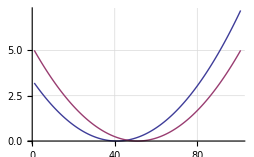

```mathematica
a = Range[0, 10, 0.1];
maxAmplitude = 5;
maxPos = 10;
curve1 = ((((1) - (maxPos / 2.0) + a)^2) / maxAmplitude);
curve2 = ((((0) - (maxPos / 2.0) + a)^2) / maxAmplitude);
ListLinePlot[{curve1, curve2}, GridLines->Automatic, GridLinesStyle->LightGray]
```

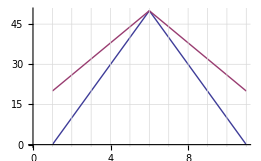

```mathematica
a = Flatten[{Range[0, 5],Range[4, 0, -1]}];
maxPos = 10;
curve1=(50-(((5-a)*50)/(maxPos/2)));
curve2=(50-(((5-a)*30)/(maxPos/2)));
ListLinePlot[{curve1, curve2}, GridLines->{Range[1,11],Automatic},
GridLinesStyle->LightGray]
```

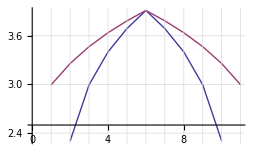

```mathematica
a = Flatten[{Range[0, 5],Range[4, 0, -1]}];
maxPos = 10;
curve1=(50-(((5-a)*50)/(maxPos/2)));
curve2=(50-(((5-a)*30)/(maxPos/2)));
ListLinePlot[{Log[curve1], Log[curve2]}, GridLines->{Range[1,11],Automatic},
GridLinesStyle->LightGray]
```